```mathematica
datasave=<||>;
SetSharedVariable[datasave];
Midi[instrument_:"Percussion",list_:0,volume_:1][note_,time_]:=
If[instrument==="Percussion",
SoundNote[If[Head@ToExpression[note]===String,
ToExpression[note],note],time,SoundVolume->volume],
SoundNote[note+list,time,If[Head@instrument===Symbol,ToString[instrument],instrument],SoundVolume->volume]];
MusicCreate[elementmatrix_,scant_:{0,∞}]:=
Module[{eventsave,soundvolume},

Sound@Flatten@Map[(
If[KeyExistsQ[datasave,#[[2;;4]]],
eventsave=datasave[#[[2;;4]]],
eventsave=ToExpression[#[[4]]][#[[2]],#[[3]]];
If[Head[eventsave]=!=SoundNote,AssociateTo[datasave, #[[2;;4]]->eventsave]];
];
soundvolume=If[Head[eventsave]===SoundNote,√(#[[5]]),#[[5]]];
Table[Sound[eventsave,{t-scant[[1]]},SoundVolume->soundvolume],{t,Cases[Flatten[{#[[1]]}],t_/;scant[[1]]<=t<=scant[[2]]]}])&,elementmatrix]]
(*默认全局变量*)
	(*默认拍性*)
	defbeat=4;

	(*默认每分钟节拍数*)
	defbpm=120;

	(*默认基准音偏移*)
	defbase=0;

	(*默认音阶*)
	defscale={"1"->0,"2"->2,"3"->4,"4"->5,"5"->7,"6"->9,"7"->11};(*简谱系统*)
	(*defscale=<|"c"->0,"d"->2,"e"->4,"f"->5,"g"->7,"a"->9,"b"->11|>;*)(*字母系统*)

	(*默认可用变调*)
	defpitchlist={"#"->1,"@"->-1,"!"->-12,"^"->12};

	(*默认变调映射:#1对应变调、#2对应原调、#3对应base*)
	defpitchmap=If[StringQ[#2](*无法解析原调*),#2,Total[#1]+#2+#3]&;
	(*默认可用节拍*)
	defbeatlist={"$"->1/3,"="->1/4,"_"->1/2,":"->2/3,"."->3/2,"-"->2};

	(*默认节拍映射*)
	defbeatmap=If[#==={},1,Total[#-UnitStep[#-1]]+UnitStep[#[[1]]-1]]&;
	(*默认可用增益*)
	defamplist={"\""->0.25,"'"->0.5,"+"->2,"*"->4};
	
	(*默认增益映射*)
	defampmap=If[#==={},1,Times@@#]&;
	(*默认可用和弦*)
		CMajor={"C"->0,"D"->2,"E"->4,"F"->5,"G"->7,"A"->9,"B"->11};
		Chord=
{"C5"->{0,7},"C8"->{0,12},"C58"->{0,7,12},"C"->{0,4,7},"Cd"->{0,3,6},"C7"->{0,4,7,10},"C9"->{0,4,7,10,14},"C9s"->{0,5,7,10,14},"Cm"->{0,3,7},"CM"->{0,4,7,11},"Cm7"->{0,3,7,10},"Cm9"->{0,3,7,10,14},"CM9"->{0,4,7,11,14}};
		defchordlist=
Association@Flatten[Outer[StringReplace[#1,"C"->#2]->(#1/.Chord)+(#2/.CMajor)&,Chord[[;;,1]],CMajor[[;;,1]]],1];

	(*默认和弦映射*)
		(*分解和弦映射*)
		Bk[n_]:=#[[n]]&
		(*转位和弦映射*)
		Iv[n_]:=Module[{list=#},list[[;;UpTo[n]]]+=12;list]&
		(*映射构造*)		
		defchordmap=
<|"a"->Bk[1],"b"->Bk[2],"c"->Bk[3],"d"->Bk[4],"e"->Bk[5],"f"->Bk[6],"s"->Identity,"u"->Iv[1],"v"->Iv[2],"w"->Iv[3],"x"->Iv[4],"y"->Iv[5],"z"->Iv[6]|>;

	(*默认音轨名称*)
	deftrackname="";
	
	(*默认控制符号*)   
		(*默认休止符*)
		defrest="0";

		(*默认跨小节符*)
		defspan=")";

		(*默认小节符*)
		defbar="|";

		(*默认方法符*)
		defmtdctr="m";
		
		(*默认音量符*)
		defvolctr="v";

		(*默认音色符*)
		definsctr="i";

		(*默认左赋值符*)
		defleftass="[";

		(*默认右赋值符*)
		defrightass="]";

		(*默认和弦符*)
		defchordctr=">";

(*默认音轨对象参数*)
	(*默认音色或渲染方式*)
	definstrument="Midi[1]";

	(*默认力度或音量*)
	defvolume=1;

	(*默认和弦环境*)
	defchord={0,4,7};

	(*默认指针时间*)
	defpointertime=0;

	(*默认启动时间*)
	defstarttime=0;
	

(*默认全局变量集合*)
defglovar=<|"beat"->defbeat,"bpm"->defbpm,"base"->defbase,"scale"->defscale,"pitchlist"->defpitchlist,"pitchmap"->defpitchmap,"beatlist"->defbeatlist,"beatmap"->defbeatmap,"amplist"->defamplist,"ampmap"->defampmap,"chordlist"->defchordlist,"chordmap"->defchordmap,"trackname"->deftrackname|>;

(*默认控制符集合*)
defctrlist=<|"rest"->defrest,"span"->defspan,"bar"->defbar,"mtdctr"->defmtdctr,"volctr"->defvolctr,"insctr"->definsctr,"leftass"->defleftass,"rightass"->defrightass,"chordctr"->defchordctr|>;

(*默认音轨对象*)
deftrack=<|"instrument"->definstrument,"volume"->defvolume,"chord"->defchord,"pointertime"->defpointertime,"starttime"->defstarttime|>;

(*默认音轨对象集合*)
deftrclist=<|deftrackname->deftrack|>;
Options[SMSPCompile]={"CChordExtend"->True};
SMSPCompile[test_,OptionsPattern[]]:=
Module[{glovar=defglovar,ctrlist=defctrlist,trclist=deftrclist,FirstSplit,NowTrack,MusicNotePitch,MusicNoteTime,MusicNoteVolume,MusicNoteSpan,MusicNote,Bar,Track,Method,Volume,Instrument,CMajor,ChordMapSet,ChordSet,Chord,TranslateNote},

FirstSplit[]:=test//StringReplace[#,{ctrlist["bar"]~~x:Repeated[DigitCharacter|","|"."]~~ctrlist["rightass"]:>" "<>ctrlist["bar"]<>"{"<>x<>"}",ctrlist["bar"]->" "<>ctrlist["bar"]<>" "}]&//StringSplit[#,Repeated[" "|"\n"]]&;

(*不可用于赋值*)
NowTrack[]:=trclist[glovar["trackname"]];

(*获取音符的音高*)
MusicNotePitch[musicnote_]:=
glovar["pitchmap"][StringCases[musicnote,glovar["pitchlist"]],StringDelete[musicnote,glovar["pitchlist"][[;;,1]]|glovar["beatlist"][[;;,1]]|glovar["amplist"][[;;,1]]|ctrlist["span"]]/.glovar["chordmap"]/.glovar["scale"]/.glovar["chordlist"]//If[MemberQ[{Function,Symbol,InterpolatingFunction},Head[#]],#[NowTrack[]["chord"]],#]&//If[ListQ[#],Cases[#,_Integer],#]&,glovar["base"]];

(*获取音符的持续时间*)
MusicNoteTime[musicnote_]:=1/glovar["bpm"] 60 glovar["beatmap"][StringCases[musicnote,glovar["beatlist"]]];

(*获取音符的音量增益*)

MusicNoteVolume[musicnote_]:=glovar["ampmap"][StringCases[musicnote,glovar["amplist"]]];
(*检测音符的跨小节情况*)
MusicNoteSpan[musicnote_]:=
(trclist[glovar["trackname"]]["pointertime"]+=(60glovar["beat"])/glovar["bpm"] StringCount[musicnote,ctrlist["span"]]);

(*翻译音符成事件*)
MusicNote[note_]:=
Module[{starttime,pitch,time},
If[(pitch=MusicNotePitch[note])===ctrlist["rest"],
trclist[glovar["trackname"]]["starttime"]+=MusicNoteTime[note];
MusicNoteSpan[note];
Nothing,
time=MusicNoteTime[note];
MusicNoteSpan[note];
starttime=NowTrack[]["starttime"];
trclist[glovar["trackname"]]["starttime"]+=time;
{starttime,pitch,time,NowTrack[]["instrument"],NowTrack[]["volume"]*MusicNoteVolume[note]}
]];

(*翻译小节符*)
Bar[input_]:=
(If[input≠"",
trclist[glovar["trackname"]]["pointertime"]=(60glovar["beat"])/glovar["bpm"] If[Length[#]==1,First[#],#]&@ToExpression[input],

trclist[glovar["trackname"]]["pointertime"]+=(60glovar["beat"])/glovar["bpm"]];
trclist[glovar["trackname"]]["starttime"]=trclist[glovar["trackname"]]["pointertime"]);
(*翻译音轨符*)
Track[input_]:=
(If[!KeyExistsQ[trclist,input],AssociateTo[trclist,input->deftrack]];
glovar["trackname"]=input);

(*翻译方法符*)
Method[input_]:=
({glovar["beat"],glovar["bpm"],glovar["base"]}=ToExpression["{"<>input<>"}"]);

(*翻译音量符*)
Volume[input_]:=(trclist[glovar["trackname"]]["volume"]=ToExpression[input]);
(*翻译音色符*)
Instrument[input_]:=(trclist[glovar["trackname"]]["instrument"]=input);


CMajor={"C"->0,"D"->2,"E"->4,"F"->5,"G"->7,"A"->9,"B"->11};

(*翻译和弦设置符*)
ChordSet[input1_,input2_]:=

If[input1==""||UpperCaseQ@StringPart[input1,1],
AssociateTo[glovar["chordlist"],
If[input1≠""&&OptionValue["CChordExtend"]&&StringPart[input1,1]=="C",StringReplacePart[input1,#,{1,1}]->ToExpression["{"<>input2<>"}"]+(#/.CMajor)&/@CMajor[[;;,1]]/.Plus[_,x_]:>x,
input1->ToExpression["{"<>input2<>"}"]
]];
trclist[glovar["trackname"]]["chord"]=glovar["chordlist"][input1],

ChordMapSet[input1,input2]
];

(*翻译和弦符*)
Chord[input_]:=(trclist[glovar["trackname"]]["chord"]=glovar["pitchmap"][StringCases[input,glovar["pitchlist"]],StringDelete[input,glovar["pitchlist"][[;;,1]]]/.glovar["chordlist"],glovar["base"]]);

(*翻译符号*)
TranslateNote[note_]:=
With[{first=StringPart[note,1],last=StringPart[note,-1]},
Catch[
(*小节符*)
If[first==ctrlist["bar"],Bar@StringDrop[note,1];Throw[Nothing]];
If[last==ctrlist["rightass"],
(*音轨符*)
If[first==ctrlist["leftass"],Track@StringTake[note,{2,-2}];Throw[Nothing]];
If[StringPart[note,2]==ctrlist["leftass"],
(*方法符*)
If[first==ctrlist["mtdctr"],Method@StringTake[note,{3,-2}];Throw[Nothing]];
(*音量符*)
If[first==ctrlist["volctr"],Volume@StringTake[note,{3,-2}];Throw[Nothing]];
(*音色符*)
If[first==ctrlist["insctr"],Instrument@StringTake[note,{3,-2}];Throw[Nothing]]]];
(*和弦符*)
If[last==ctrlist["chordctr"],
If[first==ctrlist["leftass"],ChordSet["",StringTake[note,{2,-2}]]];
If[StringContainsQ[note,ctrlist["leftass"]],
ChordSet@@StringSplit[note,{ctrlist["leftass"],last}];Throw[Nothing],
Chord@StringDrop[note,-1];Throw[Nothing]];
];
(*音色符*)
MusicNote[note]
]];
TranslateNote/@FirstSplit[]]
```

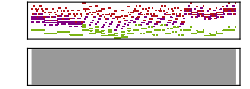

```mathematica
MusicCreate@SMSPCompile[StringReplace["
[t1] i[Midi[Flute]] v[1]
[t2] i[Midi[Piano]] v[1]
[t3] i[Midi[Cello]] v[.6] 

[t1] |0] ^C> c_ a_ ^a 0_ c_ b_ !c_ |^C> c_ a_ ^a 0_ c_ b_ !c_ |G> c_ a_ ^a 0_ c_ b_ !c_ |G> c_ a_ ^a 0_ c_ b_ !c_ |Am> c_ a_ ^a 0_ c_ b_ !c_ |Am> c_ a_ ^a 0_ c_ b_ !c_ |F> c_ a_ ^a 0_ c_ b_ !c_ |F> c_ a_ ^a 0_ c_ b_ !c_ |^C> ^b_ c_ ^b_ b_ c_ a_ c_ c_ |G> ^b_ c_ ^b_ b_ c_ a_ c_ c_ |Am> ^b_ c_ ^b_ b_ c_ a_ c_ c_ |Em> ^b_ c_ ^b_ b_ c_ a_ c_ c_ |F> ^b_ c_ ^b_ b_ c_ a_ c_ c_ |C> ^b_ c_ ^b_ b_ c_ a_ c_ c_ |Dm> ^b_ c_ ^b_ b_ c_ a_ c_ c_ |G> ^b_ c_ ^b_ b_ c_ a_ c_ c_ |^C> b_ c_ b_ ^a_ !c_ b_ !c_ ^a_ |G> b_ c_ b_ ^a_ !c_ b_ !c_ ^a_ |Am> b_ c_ b_ ^a_ !c_ b_ !c_ ^a_ |F> b_ c_ b_ ^a_ !c_ b_ !c_ ^a_ |^C> b_ c_ b_ ^a_ !c_ b_ !c_ ^a_ |G> b_ c_ b_ ^a_ !c_ b_ !c_ ^a_ |Am> b_ c_ b_ ^a_ !c_ b_ !c_ ^a_ |F> b_ c_ b_ ^a_ !c_ b_ !c_ ^a_ |^C> c_ c_ b_ c_ b_ a_ c_ ^b_ |G> c_ c_ b_ c_ b_ a_ c_ ^b_ |Am> c_ c_ b_ c_ b_ a_ c_ ^b_ |Em> c_ c_ b_ c_ b_ a_ c_ ^b_ |F> c_ c_ b_ c_ b_ a_ c_ ^b_ |G> c_ c_ b_ c_ b_ a_ c_ ^b_ |^C> c_ c_ b_ c_ b_ a_ c_ ^b_ |^C> c_ c_ b_ c_ b_ a_ c_ ^b_ |

[t2] |0] ^C> !s~ !b_ !u_ !u !s|^C> !s~ !b_ !u_ !u !s|G> !s~ !b_ !u_ !u !s|G> !s~ !b_ !u_ !u !s|Am> !s~ !b_ !u_ !u !s|Am> !s~ !b_ !u_ !u !s|F> !s~ !b_ !u_ !u !s|F> !s~ !b_ !u_ !u !s|^C> !a !b_ !b_ !c a|G> !a !b_ !b_ !c a|Am> !a !b_ !b_ !c a|Em> !a !b_ !b_ !c a|F> !a !b_ !b_ !c a|C> !a !b_ !b_ !c a|Dm> !a !b_ !b_ !c a|G> !a !b_ !b_ !c a|^C> !a_ !a_ !b_ !b_ !c_ !b_ a|G> !a_ !a_ !b_ !b_ !c_ !b_ a|Am> !a_ !a_ !b_ !b_ !c_ !b_ a|F> !a_ !a_ !b_ !b_ !c_ !b_ a|^C> !a_ !a_ !b_ !b_ !c_ !b_ a|G> !a_ !a_ !b_ !b_ !c_ !b_ a|Am> !a_ !a_ !b_ !b_ !c_ !b_ a|F> !a_ !a_ !b_ !b_ !c_ !b_ a|^C> s~ b_ b_ u s|G> s~ b_ b_ u s|Am> s~ b_ b_ u s|Em> s~ b_ b_ u s|F> s~ b_ b_ u s|G> s~ b_ b_ u s|^C> s~ b_ b_ u s|^C> s~ b_ b_ u s|

[t3] |0] ^C> !!a---|^C> !!a---|G> !!a---|G> !!a---|Am> !!a---|Am> !!a---|F> !!a---|F> !!a---|^C> !!s- !!a !!a|G> !!s- !!a !!a|Am> !!s- !!a !!a|Em> !!s- !!a !!a|F> !!s- !!a !!a|C> !!s- !!a !!a|Dm> !!s- !!a !!a|G> !!s- !!a !!a|^C> !!a !!c_ !!c_ !!a !!c|G> !!a !!c_ !!c_ !!a !!c|Am> !!a !!c_ !!c_ !!a !!c|F> !!a !!c_ !!c_ !!a !!c|^C> !!a !!c_ !!c_ !!a !!c|G> !!a !!c_ !!c_ !!a !!c|Am> !!a !!c_ !!c_ !!a !!c|F> !!a !!c_ !!c_ !!a !!c|^C> !!a--_ !!b_|G> !!a--_ !!b_|Am> !!a--_ !!b_|Em> !!a--_ !!b_|F> !!a--_ !!b_|G> !!a--_ !!b_|^C> !!a--_ !!b_|^C> !!a--_ !!b_|
","~"->" "],"CChordExtend"->True]
```